A standalone sample of how to find all the lattice cell origins for a plot region.

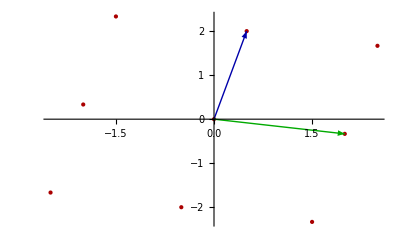

```mathematica
Module[{a,b,l, sol, points},
a = {1/2,2} ;
b = {2,-1/3} ;
l = 3 ;

sol = {n,m} /.Solve[
 ((n a + m b) . {1,0})^2 ≤ l^2
&&  ((n a + m b) . {0,1})^2 ≤ l^2
, {n,m}, Integers] ;

points = ( a #[[1]] + b#[[2]]) &/@ sol ;
ListPlot[points, PlotStyle->{Darker@Red, PointSize[Large]},
Epilog-> {Darker@Blue,Arrow[{{0,0},a}], Darker@Green, Arrow[{{0,0},b}]} ]
]
```